# Lennard-Jones Potential in Triatomic Colinear Reaction

## Part A

```mathematica
Vlj[r_]=4ϵ((σ/r)^12-(σ/r)^6);
Flj[r_]=24ϵ(2σ^12/r^13-σ^6/r^7);
```

```mathematica
ϵ=1;
σ=1;
m=1;
```

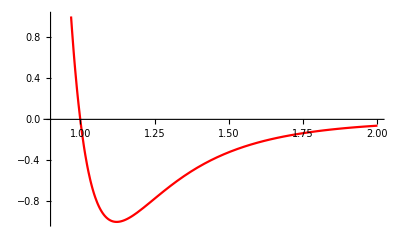

```mathematica
rMin=0.9;
rMax=2.0;
Plot[Vlj[r],{r,rMin,rMax},PlotStyle->Red]
```

```mathematica
V[rAB_,rBC_]:=Vlj[rAB]+Vlj[rBC]+Vlj[rAB+rBC]
V[rAB,rBC]
```

4 (1/rAB^12-1/rAB^6)+4 (1/rBC^12-1/rBC^6)+4 (1/(rAB+rBC)^12-1/(rAB+rBC)^6)

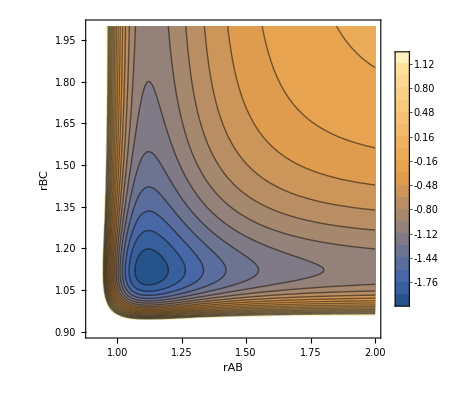

```mathematica
VPlot=ContourPlot[V[rAB,rBC],{rAB,rMin,rMax},{rBC,rMin,rMax},Contours->20,PlotLegends->Automatic,FrameLabel->{"rAB","rBC"}]
```

```mathematica
V[rAB,rBC]
```

4 (1/rAB^12-1/rAB^6)+4 (1/rBC^12-1/rBC^6)+4 (1/(rAB+rBC)^12-1/(rAB+rBC)^6)

```mathematica
NMinimize[4 (1/rAB^12-1/rAB^6)+4 (1/rBC^12-1/rBC^6)+4 (1/(rAB+rBC)^12-1/(rAB+rBC)^6),{rAB,rBC}]
```

{-2.03112,{rAB→1.12103,rBC→1.12103}}

The distances that minimize the Lennard-Jones potential are rAB=1.12103 and rBC=1.12103.

## Part B

```mathematica
def[time_,h_,xC0_,vA0_,vB0_,vC0_]:=(
nSteps=Round[time/h];
xA[0]=-3.0;
xB[0]=0;
xC[0]=xC0;
vA[0]=vA0;
vB[0]=vB0;
vC[0]=vC0;
fA[0]=-Flj[xB[0]-xA[0]]-Flj[xC[0]-xA[0]];
fB[0]=Flj[xB[0]-xA[0]]-Flj[xC[0]-xB[0]];
fC[0]=Flj[xC[0]-xA[0]]+Flj[xC[0]-xB[0]];

For[n=0,n<=nSteps,n++,
xA[n+1]=xA[n]+vA[n]h+1/2 fA[n]/m h^2;
xB[n+1]=xB[n]+vB[n]h+1/2 fB[n]/m h^2;
xC[n+1]=xC[n]+vC[n]h+1/2 fC[n]/m h^2;
fA[n+1]=-Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xA[n+1]];
fB[n+1]=Flj[xB[n+1]-xA[n+1]]-Flj[xC[n+1]-xB[n+1]];
fC[n+1]=Flj[xC[n+1]-xA[n+1]]+Flj[xC[n+1]-xB[n+1]];
vA[n+1]=vA[n]+1/2(fA[n]+fA[n+1])h/m;
vB[n+1]=vB[n]+1/2(fB[n]+fB[n+1])h/m;
vC[n+1]=vC[n]+1/2(fC[n]+fC[n+1])h/m;
]
)
time=4;
h=0.02;

xC0=1.3;

vA0=1.0;
vB0=0;
vC0=0;

def[time,h,xC0,vA0,vB0,vC0]
```

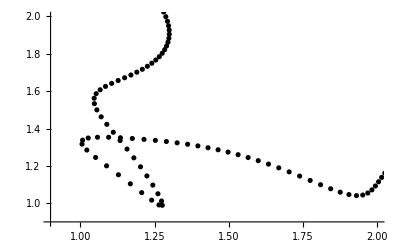

```mathematica
trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]

vAData = Table[{n h,vA[n]},{n,0,nSteps}];
ListPlot[vAData];
vBData = Table[{n h,vB[n]},{n,0,nSteps}];
ListPlot[vBData];
vCData = Table[{n h,vC[n]},{n,0,nSteps}];
ListPlot[vCData];
```

The initial conditions here correspond to particle A moving while particle B and C are at initially rest. It moves towards particle B to decrease the rAB distance, while particle B is initially at rest at x=0. Particle A transfers kinetic energy to particle B, which moves and transfers kinetic energy to particle C, which moves to increase the rBC distance.

```mathematica
animationPartB=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

## Part C

```mathematica
time=15;
h=0.02;

xC0=1.3;

vA0=0.2;
vB0=0;
vC0=0;

def[time,h,xC0,vA0,vB0,vC0]
```

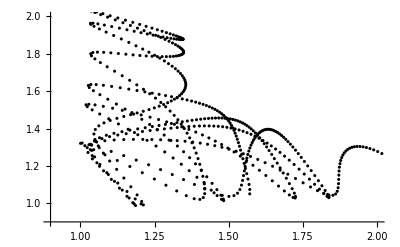

```mathematica
trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]

vAData = Table[{n h,vA[n]},{n,0,nSteps}];
ListPlot[vAData];
vBData = Table[{n h,vB[n]},{n,0,nSteps}];
ListPlot[vBData];
vCData = Table[{n h,vC[n]},{n,0,nSteps}];
ListPlot[vCData];
```

```mathematica
animationPartC=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

For the above run, we changed the initial velocity of atom A from 1.0 to 02.

The exchange reaction does not really proceed for this scenario. This can be seen in how the list plot above the animation shows the particles oscillating continuously rather than particle C moving out with the same initial speed that particle A had. Instead, particle A moves towards the B-C molecule and forms a three atom complex. The atoms vibrate which can be seen by the oscillations in the graph and animation, but once A interacts with the atoms, there is a three atom complex for the remainder of the time interval. Atom C never leaves the bond during this time and thus the reaction doesn’t proceed.

We could also change the phase of the B-C vibration without increasing the amount of vibrational energy in the BC molecule before the collision. This can be done in several ways, either with a change in initial positions or in initial velocities. We will change the initial position of particle C. Consider how the equilibrium bond distance, which is where the LJ potential is minimized, is about 1.122. The simulation we just ran had a distance of 1.3 for the B-C bond, which means the LJ potential energy was higher than its minimum possible value which would occur if C is moved a bit closer to B for its initial position. If we go past that equilibrium bond distance and move C further even more to the left to give a shorter distance, at a certain point we can match the potential energy of the current bond distance of 1.3. This will change the phase of the B-C vibration (its sinusoidal oscillation will shift) but the total energy will remain the same. To find out what bond distance will make this possible, we can refer to the LJ plot at the start of the page. The potential for the current bond distance is about -0.66 and to match that on the shorter side, we can set the distance to about 1.04.

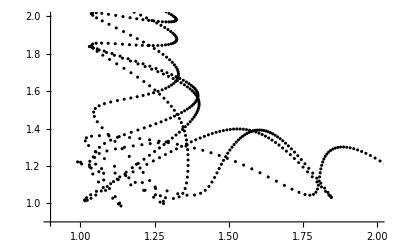

```mathematica
time=15;
h=0.02;

xC0=1.04;

vA0=0.2;
vB0=0;
vC0=0;
def[time,h,xC0,vA0,vB0,vC0]

trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]

vAData = Table[{n h,vA[n]},{n,0,nSteps}];
ListPlot[vAData];
vBData = Table[{n h,vB[n]},{n,0,nSteps}];
ListPlot[vBData];
vCData = Table[{n h,vC[n]},{n,0,nSteps}];
ListPlot[vCData];
```

```mathematica
animationPartC2=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```

Again we see that similar to the previous simulation, the exchange reaction never proceeds and instead a three atom complex forms and remains throughout the given time. The only difference now is that the phase of vibration is shifted for the B-C bond, but the reaction itself is still unsuccessful.

## Part D

Below is the simulation for initial A velocity of 5 (forces between atoms become negligible and this is like two balls hitting each other).

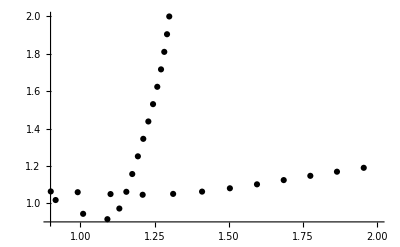

```mathematica
time=1;
h=0.02;

xC0=1.3;

vA0=5;
vB0=0;
vC0=0;
def[time,h,xC0,vA0,vB0,vC0]

trajData=Table[{xB[n]-xA[n],xC[n]-xB[n]},{n,0,nSteps}];
trajPlot=ListPlot[trajData,PlotStyle->Black,PlotStyle->PointSize[0.2],PlotRange->{{rMin,rMax},{rMin,rMax}}]

vAData = Table[{n h,vA[n]},{n,0,nSteps}];
ListPlot[vAData];
vBData = Table[{n h,vB[n]},{n,0,nSteps}];
ListPlot[vBData];
vCData = Table[{n h,vC[n]},{n,0,nSteps}];
ListPlot[vCData];
```

```mathematica
animationPartD=Animate[ListPlot[{{xA[n],0},{xB[n],0},{xC[n],0}},PlotStyle->PointSize[0.1],PlotRange->{{-rMax,rMax},{-1,1}}],{n,0,nSteps,1}]
```